```mathematica
DSolve[y'[x]==a+b*Sin[y[x]],y,x]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y→Function[{x},2 ArcTan[(-b+√((a-b) (a+b)) Tan[1/2 (√((a-b) (a+b)) x+√((a-b) (a+b)) C[1])])/a]]}}

```mathematica
2 ArcTan[-k+√(1-k^2) Tan[1/2 (√(1-k^2) ω*x)]]
```

```mathematica
2 ArcTan[-1+Tan[1/2  (t)]]
```

-2 ArcTan[1-Tan[t/2]]

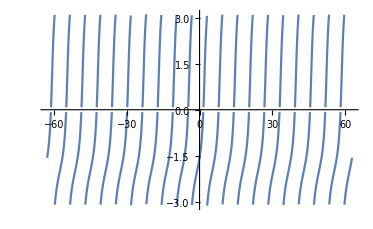

```mathematica
Plot[2ArcTan[-1+Tan[t/2]],{t,-20 π,20 π},PlotRange->Full]
```

```mathematica
Manipulate[Show[{θ=ω*t-2 ArcTan[-k+√(1-k^2) Tan[1/2 (√(1-k^2) ω*t)]];Graphics[{{Blue,Arrow[{{0,0},{Cos[ω*t],Sin[ω*t]}}]},Arrow[{{0,0},{Cos[θ],Sin[θ]}}]},Axes->True,PlotRange->{{-1,1},{-1,1}}]}],{t,0,600},{k,0,1},{ω,0,1}]
```